```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadTARCER=True;
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

TARCER 2.0, for description see the preprint hep-ph/9801383 at arxiv.org.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

0

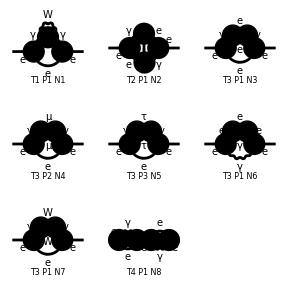

FeynArtsGraphics({e}→{e})(([T1 P1 N1] | [T2 P1 N2] | [T3 P1 N3]
[T3 P2 N4] | [T3 P3 N5] | [T3 P1 N6]
[T3 P1 N7] | [T4 P1 N8] | Null))

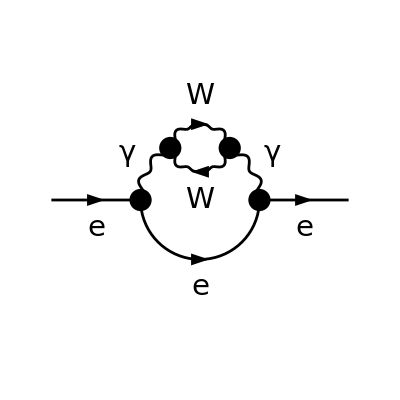

```mathematica
(* ::Subsection::*)
(*Electron self-energy*)


topsSE=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
diagsSE=InsertFields[topsSE,{F[2,{1}]}->{F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{V[2],S[_],U[_],F[1|3|4]}];
Paint[%]
Paint[DiagramExtract[diagsSE,{7}],ColumnsXRows->{3,1},SheetHeader->False,Numbering->None,ImageSize->{768,256}];
```

```mathematica
(* ::Text::*)
(*First of all we need to generate the amplitudes and convert them into FeynCalc notation.We choose l1 and l2 to be the loop momenta and p the external momentum*)


ampsSE=FCFAConvert[CreateFeynAmp[DiagramExtract[diagsSE,{7}],Truncated->True,PreFactor->-1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l1,l2},DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,SMP->True,LorentzIndexNames->{μ}]//ReplaceAll[#,SMP["m_e"]->me]&//Contract//FCTraceFactor


(* ::Text::*)
(*Calculation of the Dirac trace,tensor reduction and simplification of the Dirac algebra*)


AbsoluteTiming[ampsSE1=(ampsSE/.DiracTrace->Tr)//FCMultiLoopTID[#,{l1,l2}]&//DiracSimplify];


(* ::Text::*)
(*Simplification of the loop integrals using shifts in the loop momenta*)

SPD[p,p]=me^2;
ampsSE2=ampsSE1//FDS[#,l1,l2]&;
```

(ⅈ (γ·(2 l1-l2-2 p)).(me+γ·l1).(γ·(l1-2 l2-p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ (γ·(l1+l2-p)).(me+γ·l1).(γ·(2 l1-l2-2 p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ (γ·(-l1-l2+p)).(me+γ·l1).(γ·(l1-2 l2-p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ D (γ·(-l1+2 l2+p)).(me+γ·l1).(γ·(l1-2 l2-p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ (γ·(-l1+2 l2+p)).(me+γ·l1).(γ·(l1+l2-p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ (γ·(-l1+2 l2+p)).(me+γ·l1).(γ·(-2 l1+l2+2 p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(ⅈ (γ·(-2 l1+l2+2 p)).(me+γ·l1).(γ·(-l1-l2+p)) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))-(5 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 l1^2 e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(2 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 (l1·l2) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))+(10 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 (l1·p) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))-(2 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 l2^2 e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))-(2 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 (l2·p) e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))-(5 ⅈ γ^Lor8.(me+γ·l1).γ^Lor8 p^2 e^4)/((l1^2-me^2).(l2^2-m_W^2).(l1-p)^2.(l1-p)^2.((-l1+l2+p)^2-m_W^2))

```mathematica
(* ::Text::*)
(*IBP-Reduction using FIRE*)


ampsSE3=FIREBurn[ampsSE2,{l1,l2},{p}]//FDS[#,l1,l2]&;
```

FIREBurn: Processing integral 1 of 13; IBP-reduction done, timing: 1.857
FIREBurn: Processing integral 2 of 13; IBP-reduction done, timing: 1.754
FIREBurn: Processing integral 3 of 13; IBP-reduction done, timing: 1.402
FIREBurn: Processing integral 4 of 13; IBP-reduction done, timing: 1.598
FIREBurn: Processing integral 5 of 13; IBP-reduction done, timing: 2.045
FIREBurn: Processing integral 6 of 13; IBP-reduction done, timing: 1.783
FIREBurn: Processing integral 7 of 13; IBP-reduction done, timing: 1.386
FIREBurn: Processing integral 8 of 13; IBP-reduction done, timing: 1.568
FIREBurn: Processing integral 9 of 13; IBP-reduction done, timing: 2.997
FIREBurn: Processing integral 10 of 13; IBP-reduction done, timing: 4.966
FIREBurn: Processing integral 11 of 13; IBP-reduction done, timing: 3.094
FIREBurn: Processing integral 12 of 13; IBP-reduction done, timing: 2.102
FIREBurn: Processing integral 13 of 13; IBP-reduction done, timing: 5.386

```mathematica
(* ::Text::*)
(*Nicer form*)


ampsSE4=ampsSE3//Collect2[#,{FeynAmpDenominator},Factoring->FullSimplify]&;


(* ::Text::*)
(*This is Sigma_2V(p^2) up to the 1/(2Pi)^2D prefactor*)


resSE=Cancel[ampsSE4/(-I FCI[(GSD[p])])]//FullSimplify;


(* ::Subsection::*)
(*Check with the literature*)


(* ::Text::*)
(*Check with Eq.5.51 from Grozin's Lectures on QED and QCD (hep-ph/0508242)*)
```

```mathematica
tfiamp0=resSE//ToTFI[#,l1,l2,p]&;
SEFIRE=Simplify[TarcerRecurse[tfiamp0]];
```

```mathematica
(*SetOptions[DiracSlash,Dimension->D,FeynCalcInternal->True];SetOptions[DiracTrace,DiracTraceEvaluate->True];*)
fullamp0=(ampsSE2)//DiracSimplify//FCMultiLoopTID[#,{l1,l2}]&//DiracSimplify;
tfiamp0=fullamp0//ToTFI[#,l1,l2,p]&;
SE=Simplify[TarcerRecurse[tfiamp0]];
```

```mathematica
SE
```

1/(4 (D-5))ⅈ e^4 ((16 (2 D-3) γ·p (me-m_W) (me+m_W) J_({2,m_W}{2,m_W}{1,me})^(D) m_W^2)/((D-4) (3 D-8) me^2)-(32 (2 D-3) γ·p (me-m_W) (me+m_W) J_({2,m_W}{2,m_W}{2,me})^(D) m_W^2)/((D-6) (3 D-10))-(256 (2 D-3) γ·p (me-m_W) (me+m_W) (2 me^2-m_W^2) J_({3,me}{2,m_W}{1,m_W})^(D) m_W^2)/((D-6) (3 D-10) me^2)-(16 (3 (9 D^4-99 D^3+386 D^2-616 D+320) me^3+γ·p ((-27 D^4+315 D^3-1306 D^2+2280 D-1432) me^2+2 (6 D^3-65 D^2+204 D-180) m_W^2)) J_({3,m_W}{1,m_W}{1,me})^(D) m_W^2)/((D-6) (D-4) (3 D-10) (3 D-8) me^2)-(64 (2 D-3) γ·p (me-m_W) (me+m_W) J_({3,m_W}{2,me}{1,m_W})^(D) m_W^2)/((D-6) (3 D-10))-(8 γ·p ((9 D^3-63 D^2+151 D-123) me^2-5 (2 D^3-13 D^2+27 D-18) m_W^2) J_({1,m_W}{1,m_W}{1,me})^(D))/((D-6) me^4)-(4 (3 (3 D^4-44 D^3+219 D^2-418 D+240) me^5+γ·p ((-33 D^4+328 D^3-1281 D^2+2536 D-2220) me^4+(77 D^4-760 D^3+2667 D^2-3948 D+2124) m_W^2 me^2-8 (2 D^4-19 D^3+62 D^2-81 D+36) m_W^4)) J_({2,me}{1,m_W}{1,m_W})^(D))/((D-6) (D-4) (3 D-8) me^4)-(4 (3 (3 D^4-44 D^3+219 D^2-418 D+240) me^5+γ·p ((-9 D^4+164 D^3-1073 D^2+2960 D-2892) me^4+(-87 D^4+846 D^3-2829 D^2+3796 D-1716) m_W^2 me^2+8 (12 D^4-124 D^3+457 D^2-711 D+396) m_W^4)) J_({2,m_W}{1,m_W}{1,me})^(D))/((D-6) (D-4) (3 D-8) me^4)+(16 (γ·p (2 (D-4)^2 (6 D^2-25 D+24) me^6+(-15 D^4+16 D^3+616 D^2-2296 D+2104) m_W^2 me^4+2 (42 D^4-377 D^3+1095 D^2-1088 D+228) m_W^4 me^2-8 (6 D^4-59 D^3+199 D^2-266 D+120) m_W^6)-3 (9 D^4-99 D^3+386 D^2-616 D+320) me^5 m_W^2) J_({2,m_W}{2,me}{1,m_W})^(D))/((D-6) (D-4) (3 D-10) (3 D-8) me^4)+(16 (γ·p (2 (16 D^2-82 D+87) me^4+(-35 D^2+165 D-166) m_W^2 me^2+4 (2 D^2-9 D+9) m_W^4)-3 (3 D^2-13 D+10) me^3 m_W^2) J_({3,me}{1,m_W}{1,m_W})^(D))/((D-6) (3 D-10) me^2)+((D-2)^2 γ·p ((21 D^3-262 D^2+1027 D-1266) me^2-4 (6 D^3-43 D^2+99 D-72) m_W^2) (A_{1,m_W}^(D))^2)/((D-6) (D-3) (3 D-8) me^4 m_W^2)+1/((D-6) (D-4) (D-3) (3 D-10) (3 D-8) me^6 m_W^2)(D-2) (3 (9 D^3-63 D^2+134 D-80) me^3 ((2 D^3-23 D^2+84 D-92) me^2+8 (D^2-7 D+12) m_W^2)-(D-2) γ·p ((66 D^5-1187 D^4+8503 D^3-30218 D^2+53148 D-36952) me^4+(-129 D^5+1862 D^4-10411 D^3+27766 D^2-34444 D+15096) m_W^2 me^2+4 (18 D^5-245 D^4+1291 D^3-3278 D^2+3996 D-1872) m_W^4)) A_{1,me}^(D) A_{1,m_W}^(D))

```mathematica
SEFIRE2=SEFIRE/.D->4-2ϵ
```

-1/(32 me^4 (-2 ϵ-2) ϵ γ·p)e^4 (-((2-2 ϵ)^2 (γ·p ((-11 (4-2 ϵ)^2+74 (4-2 ϵ)-95) m_W^2+me^2 (9 (4-2 ϵ)^3-161 (4-2 ϵ)^2+859 (4-2 ϵ)-1443))+3 me (3-2 ϵ) ((2 (4-2 ϵ)^2-17 (4-2 ϵ)+35) m_W^2+me^2 (5 (4-2 ϵ)^2-44 (4-2 ϵ)+99))) (A_{1,m_W}^(4-2 ϵ))^2)/((-2 ϵ-1) (1-2 ϵ) m_W^2)-(2 (2-2 ϵ) A_{1,me}^(4-2 ϵ) (3 me (3-2 ϵ) (me^2 (4 (4-2 ϵ)^3-47 (4-2 ϵ)^2+173 (4-2 ϵ)-190)-((4-2 ϵ)^3-24 (4-2 ϵ)^2+133 (4-2 ϵ)-210) m_W^2)-(2-2 ϵ) γ·p (me^2 (12 (4-2 ϵ)^3-153 (4-2 ϵ)^2+638 (4-2 ϵ)-865)-((4-2 ϵ)^3-25 (4-2 ϵ)^2+91 (4-2 ϵ)-3) m_W^2)) A_{1,m_W}^(4-2 ϵ))/((-2 ϵ-1) (1-2 ϵ) m_W^2)+2 (γ·p ((-33 (4-2 ϵ)^2+145 (4-2 ϵ)-152) m_W^2+me^2 (-15 (4-2 ϵ)^3+146 (4-2 ϵ)^2-475 (4-2 ϵ)+552))+3 me (3 (4-2 ϵ)^2-11 (4-2 ϵ)+8) ((2 (4-2 ϵ)-7) m_W^2+3 me^2 (-2 ϵ-1))) J_({1,m_W}{1,m_W}{1,me})^(4-2 ϵ)+8 (me-m_W) (m_W+me) (γ·p ((19-11 (4-2 ϵ)) m_W^2+me^2 (-12 (4-2 ϵ)^2+93 (4-2 ϵ)-173))+3 me (3-2 ϵ) ((2 (4-2 ϵ)-7) m_W^2+me^2 (4 (4-2 ϵ)-19))) J_({2,m_W}{1,m_W}{1,me})^(4-2 ϵ))

```mathematica
Coefficient[Series[SEFIRE2,{ϵ,0,0}],ϵ,0]/.ϵ->0
```

1/(32 me^4 γ·p)e^4 (1/2 (-1/m_W^2 2 (A_{1,m_W}^(4) (A_{1,me}^(4) (2 (-18 me m_W^2+50 m_W^2 γ·p+54 me^3-14 me^2 γ·p)-2 (-186 me m_W^2+194 m_W^2 γ·p+162 me^3-26 me^2 γ·p))+4 TAI^(1,0,(0 | 0))(4,0,(1 | me)) (-18 me m_W^2+50 m_W^2 γ·p+54 me^3-14 me^2 γ·p))+4 TAI^(1,0,(0 | 0))(4,0,(1 | m_W)) A_{1,me}^(4) (-18 me m_W^2+50 m_W^2 γ·p+54 me^3-14 me^2 γ·p))+(-16 TAI^(1,0,(0 | 0))(4,0,(1 | m_W)) (-9 me m_W^2+25 m_W^2 γ·p+27 me^3-7 me^2 γ·p) A_{1,m_W}^(4)-(8 (-9 me m_W^2+25 m_W^2 γ·p+27 me^3-7 me^2 γ·p)-4 (24 me m_W^2+28 m_W^2 γ·p+54 me^3-6 me^2 γ·p)) (A_{1,m_W}^(4))^2)/m_W^2+2 ((-222 me m_W^2+238 m_W^2 γ·p+18 me^3+54 me^2 γ·p) J_({1,m_W}{1,m_W}{1,me})^(4)-2 TJI^(1,0,(0 | 0
0 | 0
0 | 0))(4,me^2,(1 | m_W
1 | m_W
1 | me)) (36 me m_W^2-100 m_W^2 γ·p-108 me^3+28 me^2 γ·p))+8 (me-m_W) (m_W+me) ((-42 me m_W^2+22 m_W^2 γ·p-54 me^3+6 me^2 γ·p) J_({2,m_W}{1,m_W}{1,me})^(4)-2 TJI^(1,0,(0 | 0
0 | 0
0 | 0))(4,me^2,(2 | m_W
1 | m_W
1 | me)) (9 me m_W^2-25 m_W^2 γ·p-27 me^3+7 me^2 γ·p)))+1/2 (-(4 (-9 me m_W^2+25 m_W^2 γ·p+27 me^3-7 me^2 γ·p) (A_{1,m_W}^(4))^2)/m_W^2-(4 A_{1,me}^(4) (-18 me m_W^2+50 m_W^2 γ·p+54 me^3-14 me^2 γ·p) A_{1,m_W}^(4))/m_W^2-2 (36 me m_W^2-100 m_W^2 γ·p-108 me^3+28 me^2 γ·p) J_({1,m_W}{1,m_W}{1,me})^(4)-8 (me-m_W) (m_W+me) (9 me m_W^2-25 m_W^2 γ·p-27 me^3+7 me^2 γ·p) J_({2,m_W}{1,m_W}{1,me})^(4)))